```mathematica
ClearAll["Global`*"];
ClearAll[m];
(*参数parameters*)
a=1/10;
Qm=5/10;
μ=10000;
```

```mathematica
(*度规Metric*)
A=2/Pi μ;
m[r_]:=1-Qm^2/(2r)+(A Qm^4)/(40 r^5);
Σ=r^2+a^2 Cos[θ]^2;
Δ=r^2-2 m[r]r+a^2;
g={{-(1-(2 m[r]r)/Σ),0,0,-(1/Σ)2 a m[r]r Sin[θ]^2},{0,Σ/Δ,0,0},{0,0,Σ,0},{-(1/Σ)2 a m[r]r Sin[θ]^2,0,0,(r^2+a^2+(1/Σ)2 m[r] a^2 r Sin[θ]^2)Sin[θ]^2}};(*g_{\mu\nu}*)
Ig={{(-((a^2+r^2)^2-a^2 (a^2-2 m[r]r+r^2) Sin[θ]^2))/((r^2+a^2 Cos[θ]^2)(a^2-2 m[r]r+r^2)),0,0,-(2 a m[r]r)/((r^2+a^2 Cos[θ]^2)(a^2-2 m[r]r+r^2))},{0,(a^2-2 m[r]r+r^2)/(r^2+a^2 Cos[θ]^2),0,0},{0,0,1/(r^2+a^2 Cos[θ]^2),0},{-(2 a m[r]r)/((r^2+a^2 Cos[θ]^2)(a^2-2 m[r]r+r^2)),0,0,((a^2-2 m[r]r+r^2)-a^2 Sin[θ]^2)/((r^2+a^2 Cos[θ]^2)(a^2-2 m[r]r+r^2)Sin[θ]^2)}};(*g^{\mu\nu}*)
(*电磁场ElectroMagnetic Field*)
F01=-Qm(2a r Cos[θ])/((r^2+a^2 Cos[θ]^2)^2);
F02=-Qm((r^2-a^2 Cos[θ]^2)a Sin[θ])/((r^2+a^2 Cos[θ]^2)^2);
F={{0,F01,F02,0},{-F01,0,0,F01 a Sin[θ]^2},{-F02,0,0,(r^2+a^2)/a F02},{0,-F01 a Sin[θ]^2,-(r^2+a^2)/a F02,0}};(*F_{\mu\nu}*)
trF=-2(F01^2-F02^2/(a^2 Sin[θ]^2))//Simplify;(*\mathcal{F}*)
trG=-4(F01 F02)/(a Sin[θ])//Simplify;(*\mathcal{G}*)
FF=-Simplify[Ig.Simplify[F.Simplify[Ig.F.Ig]]];(*F^{\mu\alpha}F^\nu\,_\alpha*)
(*有效度规和哈密顿量the Effective Metric and Hamiltonian*)
Ω1=((7μ)/8)^2 trG/(4Pi);
Ω2=-(3μ)/32+((17 μ^2)/16)trF/(4Pi);
Ω3=-(μ/2)^2 trG/(4Pi);
(*Ωplus=-1/(2Ω1)(Ω2-√(Ω2^2-4Ω1 Ω3))//Simplify;*)
Ωminus=-1/(2Ω1)(Ω2+√(Ω2^2-4Ω1 Ω3))//Simplify;
(*Kplus=(-1/4+μ/(8Pi)trF+(7μ)/(32Pi)Ωplus*trG)*Ig+μ/(2Pi)*FF;*)
Kminus=(-1/4+μ/(8Pi)trF+(7μ)/(32Pi)Ωminus*trG)*Ig+μ/(2Pi)*FF//Simplify;
IK=Inverse[Kminus];
QQ={qt,qr,qθ,qϕ};
H=1/2(7*Sum[Kminus[[i,j]]QQ[[i]]QQ[[j]],{i,1,4},{j,1,4}]);
(*运动方程EoM*)
du={td,rd,θd,ϕd,qrd,qθd};
td=D[H,qt];
rd=D[H,qr];
θd=D[H,qθ];
ϕd=D[H,qϕ];
qrd=-D[H,r];
qθd=-D[H,θ];
Deom=du/.{qt->-EE,qϕ-> LL,t-> t[λ],r-> r[λ],θ-> θ[λ],ϕ-> ϕ[λ],qr-> qr[λ],qθ-> qθ[λ]};
(*\delta*)
δ1=(μ trF)/(4Pi)/.{t-> t[λ],r-> r[λ],θ-> θ[λ],ϕ-> ϕ[λ]};
δ2=(7μ trG^2)/(16Pi trF)/.{t-> t[λ],r-> r[λ],θ-> θ[λ],ϕ-> ϕ[λ]};
δ3=-((a^2  Qm^2 μ Cos[θ]^2(a^10 Cos[θ]^10+6 a^8 Cos[θ]^8 r^2+14 a^6 Cos[θ]^6 r^4+44 a^4 Cos[θ]^4 r^6+17 a^2 Cos[θ]^2 r^8+30 r^10) )/((a^2 Cos[θ]^2+r^2)^6 (2 π r^4-Qm^2 μ)))/.{t-> t[λ],r-> r[λ],θ-> θ[λ],ϕ-> ϕ[λ]};
δ4=(2 a^2 Qm^2 μ Cos[θ]^2 (12 r^12+95 a^2 r^10 Cos[θ]^2+82 a^4 r^8 Cos[θ]^4+82 a^6 r^6 Cos[θ]^6+48 a^8 r^4 Cos[θ]^8+15 a^10 r^2 Cos[θ]^10+2 a^12 Cos[θ]^12))/(π (r^2+a^2 Cos[θ]^2)^6 (3 A Qm^2 r^2-4 r^6+2 a^2 A Qm^2 Cos[θ]^2))/.{t-> t[λ],r-> r[λ],θ-> θ[λ],ϕ-> ϕ[λ]};
δ5=((a^2 Cos[θ]^2 Qm^2 μ)/((a^2 Cos[θ]^2+r^2)^6 (-20 π^2 r^8 (2 a^2+Qm^2+2 (-1+r) r)+4 π Qm^2 r^2 (5 a^4 Cos[θ]^2+5 a^2 (2+Cos[θ]^2) r^2+r^2 (3 Qm^2+5 r (-1+2 r))) μ-Qm^6 μ^2)))(20 a^14 Cos[θ]^12 π r^2+20 a^12 Cos[θ]^10 (8+Cos[θ]^2) π r^4+60 π r^14 (5 Qm^2+r (-10+7 r))-30 Qm^4 r^10 μ+a^2 r^8 (420 π r^6+Cos[θ]^2 (10 π r^4 (17 Qm^2+2 r (-17+56 r))-17 Qm^4 μ))+4 a^4 Cos[θ]^2 r^6 (280 π r^6+Cos[θ]^2 (5 π r^4 (22 Qm^2+r (-44+63 r))-11 Qm^4 μ))+2 a^6 Cos[θ]^4 r^4 (630 π r^6+Cos[θ]^2 (10 π r^4 (7 Qm^2+2 r (-7+24 r))-7 Qm^4 μ))+a^10 Cos[θ]^8 (540 π r^6+Cos[θ]^2 (10 π r^4 (Qm^2+2 r (-1+8 r))-Qm^4 μ))+6 a^8 Cos[θ]^6 r^2 (160 π r^6+Cos[θ]^2 (10 π r^4 (Qm^2+r (-2+9 r))-Qm^4 μ)))/.{t-> t[λ],r-> r[λ],θ-> θ[λ],ϕ-> ϕ[λ]};
Print["-------------------------------Done 1-------------------------------------------"]
```

-------------------------------Done 1-------------------------------------------

```mathematica
(*定义Kerr度规*)
ClearAll[MetricDown];
MetricDown[{t_,r_,θ_,ϕ_}]:=Module[{tt,rr,θθ,ϕϕ,tϕ,Σ,Δ},
Σ=r^2+a^2 Cos[θ]^2;
Δ=r^2-2m[r] r+a^2;
tt=-(1-(2 m[r] r)/Σ);
rr=Σ/Δ;
θθ=Σ;
ϕϕ=(r^2+a^2+(2 m[r] a^2 r Sin[θ]^2)/Σ)Sin[θ]^2;
tϕ=-(2 a m[r]r Sin[θ]^2)/Σ;
({{tt, 0, 0, tϕ}, {0, rr, 0, 0}, {0, 0, θθ, 0}, {tϕ, 0, 0, ϕϕ}})];
(*把θ变到0~π，把ψ变到0~2π*)
ClearAll[WrapAngle];
WrapAngle[a1_,a2_]:=Module[{x1=a1,x2=a2},
While[x1>π,x1=x1-2π];
While[x1<-π,x1=x1+2π];
If[x1<0,x1=-x1;x2=x2+π];
While[x2≥2π,x2=x2-2π];
While[x2<0,x2=x2+2π];
{x1,x2}];
(*ZAMO标架场*)
ClearAll[LocalTetrads];
LocalTetrads[pos_,metric_]:=Module[{e0,e1,e2,e3,gtt,grr,gθθ,gϕϕ,gtϕ},
{gtt,grr,gθθ,gϕϕ,gtϕ}=Extract[metric,{{1,1},{2,2},{3,3},{4,4},{1,4}}];
e0=√(-(gϕϕ/(gtt gϕϕ-gtϕ gtϕ))){1,0,0,-(gtϕ/gϕϕ)};(*Subscript[e, t]*)
e1={0,-(1/(√grr)),0,0};(*-Subscript[e, r]*)
e2={0,0,1/(√gθθ),0};(*Subscript[e, θ]*)
e3={0,0,0,-(1/(√gϕϕ))};(*-Subscript[e, ϕ]*)
{e0,e1,e2,e3}];
(*得到光线的初始方向以及相对应的上标四速度*)
ClearAll[GetIniMomentum];
GetIniMomentum[metric_,pos_,fov_,npix_][i_,j_]:=Module[{λdot,xscr,yscr,θx,ψx,vel,e0,e1,e2,e3,κ,momentum,IKn},
{xscr,yscr}=(2Tan[fov/2]/npix)(#-(1/2)(npix+1))&/@{i,j};
{θx,ψx}=WrapAngle[2ArcTan[(√(xscr^2+yscr^2))/2],ArcTan[-yscr,-xscr]];
vel=N@{Cos[θx],Sin[θx]Cos[ψx],Sin[θx]Sin[ψx]};
{e0,e1,e2,e3}=N@LocalTetrads[pos,metric];
λdot=-(vel[[1]]e1+vel[[2]]e2+vel[[3]]e3);
IKn=IK/.{t-> pos[[1]],r->pos[[2]],θ-> pos[[3]],ϕ->pos[[4]]};(*末态四速度的空间分量,时间分量κ>0(指向未来)，具体大小由四速度模方等于0确定*)
κ=1/(e0.IKn.e0)*(-e0.IKn.λdot+√((e0.IKn.λdot)^2-(e0.IKn.e0)(λdot.IKn.λdot)));
If[κ<0,Print["相机距黑洞过近Too close to the black hole"];Abort[];];
λdot=κ e0+λdot;
momentum=IKn.λdot;
momentum];
(*数值求解单条光线的方程*)
ClearAll[TraceSingleRay];
TraceSingleRay[pos_,fov_,npix_][i_,j_]:=Module[{λF=3000,eqns,E0,L0,idata,initialConditions,sol,frame,momentum,eom,data,tag,rF,delta},
momentum=GetIniMomentum[MetricDown[pos],pos,fov,npix][i,j];
{E0,L0}={-momentum[[1]],momentum[[4]]};
idata=Join[pos,{momentum[[2]],momentum[[3]]}];
initialConditions=Thread[{t[0],r[0],θ[0],ϕ[0],qr[0],qθ[0]}==idata];
eom=Thread[{t'[λ],r'[λ],θ'[λ],ϕ'[λ],qr'[λ],qθ'[λ]}==Deom];
eqns=N[Join[eom,initialConditions]/.{EE-> E0,LL-> L0}];
{sol,data}=Reap[NDSolve[eqns,{t,r,θ,ϕ,qr,qθ},{λ,0,-λF},Method->{"EventLocator", "Event"->{r[λ]-1.01horizon,r[λ]-10000horizon},"EventAction":>{Throw[λF =-λ,"StopIntegration"],Throw[λF =-λ,"StopIntegration"]}},
EvaluationMonitor:>(Sow[Evaluate[Abs[δ1]],del1];Sow[Evaluate[Abs[δ2]],del2];Sow[Evaluate[Abs[δ3]],del3];Sow[Evaluate[Abs[δ4]],del4];Sow[Evaluate[Abs[δ5]],del5])]];
rF=r[-λF]/.sol[[1]];
If[rF<3 horizon,tag=0,tag=1];(*tag=1表示光线可以出射*)
delta=tag*(Max/@data);
Join[{r[-λF],θ[-λF],ϕ[-λF],qr[-λF],qθ[-λF],E0,L0},delta]/.sol[[1]]]
(*搞一个进度条查看跑了多少*)
ClearAll[MonitorParallelTable];
MonitorParallelTable[expr_,npix_]:= Module[{res,iterCount=npix^2,progress=0},
  SetSharedVariable[progress];
  res=Monitor[ParallelTable[(progress++;expr[j,i]),{i,1,npix},{j,1,npix}],
(*i对应行,画图时是y坐标,j对应列,画图时是x坐标。但是TraceSingleRay的参数中,第一个元素是x坐标,第二个元素是y坐标,所以看起来有点奇怪*)
    Column[{ToString@progress<>" of "<>ToString@iterCount,ProgressIndicator[progress,{0,iterCount}]},Alignment->Center]];
  UnsetShared[progress];
res];
(*跑所有的点*)
ClearAll[TraceRay];
TraceRay[pos_,fov_,npix_]:=MonitorParallelTable[TraceSingleRay[pos,fov,npix],npix];
Print["-------------------------------Done 2-------------------------------------------"]
```

-------------------------------Done 2-------------------------------------------

```mathematica
(*准备就绪，开始跑函数*)
ClearAll[result,resultplot]
horizon=Max[r/.NSolve[r^2-2m[r] r+ a^2==0,r,Reals]];
pos={0,80,π/2-0.01,0};
fov=π/5;
npix=64;(*should be even*)
result=TraceRay[pos,fov,npix];
resultplot=result[[All,All,1;;3]];
```

```mathematica
(*验证一下末态哈密顿量*)
icheck=10;(*检查点(icheck,icheck)的哈密顿量是否为0*)
Print[H/.{r->result[[icheck,icheck,1]],θ->result[[icheck,icheck,2]],qr->result[[icheck,icheck,4]],qθ->result[[icheck,icheck,5]],qt->-result[[icheck,icheck,6]],qϕ->result[[icheck,icheck,7]]}];
```

7.05313×10^-7

```mathematica
split=π/18;
ClearAll[GetColor];
ClearAll[GetClosestAngle];
{θ0,ϕ0}={pos[[3]],pos[[4]]};
GetClosestAngle[x_]:=With[{q=IntegerPart[x/split]},Min[(q+1)split-x,x-q split]];
GetColor[{rF_,θFx_,ϕFx_}]:=Module[{θF,ϕF},
If[rF<3 horizon,Return[Black]];(*此处原本是rF<1.1 horizon0,但好像违反这个条件不足以保证光子可以出射*)
{θF,ϕF}={θFx,ϕFx};
{n1,n2}={Sin[θF] Sin[ϕF-ϕ0],-Cos[θ0]Sin[θF] Cos[ϕF-ϕ0]+Sin[θ0]Cos[θF]};
{theta,psi}=WrapAngle[ArcSin[n2],ArcSin[n1]];(*注意theta和psi都是纬线*)
Which[GetClosestAngle[theta]≤0.01||GetClosestAngle[psi]≤0.01,Return[Black],n1>0&&n2>0,RGBColor[{225,227,76}/255](*yellow*),n1>0&&n2<0,RGBColor[{62,55,129}/255](*blue*),n1<0&&n2< 0,RGBColor[{240,138,122}/255](*red*),n1<0&&n2>0,RGBColor[{77,178,71}/255](*green*)]];
```

{0.0554737,0.000125556,0.000141053,0.0000626476,0.0000993739}

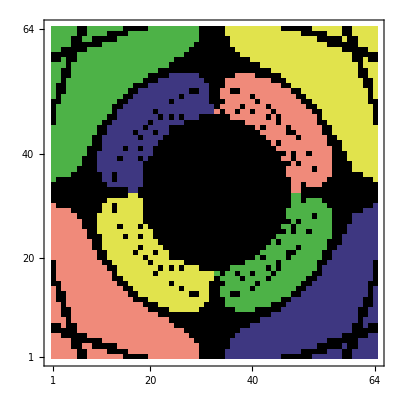

-Graphics-

```mathematica
(*Print Delta*)
Print[{ Max[result[[All,All,8]]], Max[result[[All,All,9]]], Max[result[[All,All,10]]], Max[result[[All,All,11]]], Max[result[[All,All,12]]]}]
MatrixPlot[Map[GetColor,resultplot,{2}],DataReversed->{True,False},AspectRatio->1]
(*画Shadow*)
MatrixPlot[Map[If[#<3horizon,1,0]&,resultplot⟦All,All,1⟧,{2}],ColorFunction->"Monochrome",DataReversed->{True,False},AspectRatio->1]
```